## Define Functions and Parameters

```mathematica
(* Calculating Euclidean Distances *)
CalculateEuclideanDistances[coordinatesSet_]:=Table[N[EuclideanDistance[coordinatesSet[[i]],#]]&/@coordinatesSet,{i,1,coordinatesSet//Length }]
(* Exponential Kernel *)
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
```

```mathematica
(*Markov - Calculates fraction of time mosquitoes spend at each network node, given a Markov process
migrationProbabilities = transitions probability matrix, calculated using Euclidean distances and a Kernel *)
CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
```

```mathematica
(*Networks Plot*)
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[EdgesStyleList]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,PlotTheme->"LakeNetwork",EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
(*Plots Styles*)
Themes`AddThemeRules["LakeMatrixPlot"
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,ImageSize->250
,PlotRangePadding->0
]
Themes`AddThemeRules["LakeNetwork",
,EdgeShapeFunction->edgeshape2
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
,ImageSize -> 500
,ImagePadding->25
,LineThickness -> .0075
,VariableStyle->"Both"
,VertexCoordinates ->sampledCoordinates
,VertexSize ->.01
,VertexLabelStyle->.001
]
(*USES GLOBALS!*)
GraphPlotWrapper[migrationMatrix_,max_,vertexSize_,vertexStyle_]:= GraphTransitionsFrequenciesWithMax[
  {
migrationMatrix,
ToString /@ Range[Length[migrationMatrix]]
   }, max
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->imageSize
,LineThickness->lineThickness
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> vertexSize
,VertexStyle->vertexStyle
,VertexLabelStyle->.0001
  ]
```

LakeMatrixPlot

LakeNetwork

```mathematica
(* Define edge Chop Threshold *) 
edgeChopThreshold = 10^-1.5;
```

```mathematica
(* Analytic expression for VCI matrix calculations *)
vciAnalytic[ms_,init_,EIP_,siteType_]:=DiagonalMatrix[(init[[;;-2]]*(2.-siteType) + (init[[;;-2]]*(siteType-1.)).ms).Inverse[(IdentityMatrix[Length[ms]] - MatrixPower[ms,2])]]. MatrixPower[ms,Ceiling[EIP/2.]*2].
Inverse[(IdentityMatrix[Length[ms]] - ms)].
DiagonalMatrix[(2-siteType)]
```

## Step 1 : Import Landscape Data

```mathematica
(* Read in our data *)
mosHabitats = Import["/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron/MosHabitats_3.csv"];
(* 
1 if a blood feeding site,
0 if an egg laying site
*)
siteType = If[#=="houses",1,2]&/@mosHabitats[[2;;,2]];
mosHabitats = 5000*mosHabitats[[2;;, 3;;]];
nHouses = Count[siteType,1];
```

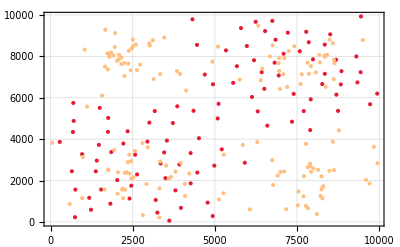

```mathematica
(* A beautiful plot *)
colors = ColorData["BrightBands", #]&/@Range[0,1,1]//Flatten;
ListPlot[mosHabitats[[Position[siteType,#]//Flatten]]&/@{1,2}, PlotStyle->colors,PlotTheme->{"Grid","Frame"}]
```

## Step 2 : Generate interaction matrices, based on distance kernel and site type masking

```mathematica
networkDimension = 2; (* Two types of sites for now *)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(* Define which inter-type transitions are allowed *)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
MatrixForm[penalizationsMatrix]
```

(0 | 1
1 | 0)

```mathematica
(* Calculate distances between everything *)
euclideanDistances = CalculateEuclideanDistances[mosHabitats];
(* Given the Euclidean distances, what are the probabilities of moving *)
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
```

```mathematica
(* Define the expanded Mask *)
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@siteType,{i,siteType}]; 
(* Re-weighting all edges according to the movement kernel and penalization mask.*)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
```

```mathematica
(* Adding in mosquito death *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
```

```mathematica
(*init = Join[Table[1./Length[migrationDimensionalMatrix],{i,1,Length[migrationDimensionalMatrix]}],{0}];*)
init =#&/@If[#==1,0.,1.]&/@siteType/Count[siteType,2];
init = Join[init,{0}];
EIP = 10;
```

```mathematica
vci = vciAnalytic[ms, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vci[[;;nHouses,;;nHouses]]//Transpose]
{Mean[%],Variance[%]}
```

{0.15563,0.0168962,0.14792,0.172916,0.0668245,0.00227982,0.000255956,0.0145495,0.00500721,0.0439795,0.0000160817,0.00361672,0.0000164016,0.0413025,0.00325373,0.000116463,0.206979,4.25603×10^-7,9.17627×10^-7,0.0224537,2.72372×10^-6,0.0000277221,0.0353851,0.168865,0.0000620152,0.115344,0.011375,0.0739964,0.0549948,0.107903,0.00567905,2.261×10^-7,0.0537045,0.0591769,0.0489158,0.000117811,0.003349,0.122247,0.000836958,3.12937×10^-7,0.00203082,4.32269×10^-8,6.95052×10^-6,0.111691,3.28695×10^-8,0.106726,0.000267842,0.187926,0.107833,0.0526572,0.000028373,0.227496,0.0675847,0.000242064,0.0887221,0.0362118,0.0116701,0.146896,0.000908192,0.640195,0.0666148,0.103558,1.20205×10^-6,4.53244×10^-8,1.4463×10^-6,7.81627×10^-7,0.35279,0.258579,0.31188,0.0000302283,0.00156358,0.102027,0.804135,0.109346,0.00102403,0.303401,0.0000837077,0.114478,0.121901,0.0238806,0.00398357,0.00247346,0.000160725,0.00155155,0.138763,0.1236,1.12422×10^-6,0.971985,0.0000170713,0.882624,0.0283553,0.00065961,5.10573×10^-6,0.0575674,0.179527,0.0522491,0.0131903,0.00023848,0.00544147,0.0000368467}

{0.0869281,0.0295059}

## Step 3: Clustering Analysis

```mathematica
(* Try some clustering, based on neighborhood contraction *)
clusteredCoordinates=FindClusters[mosHabitats,Method->"NeighborhoodContraction"];
(* List of site indices *)
clustersStrings=Table[ToString/@Flatten[Position[mosHabitats,#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}];
(* Vector of site IDs for each site *)
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[mosHabitats]];
```

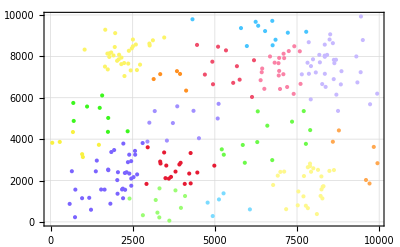

```mathematica
(* A beautiful plot *)
colors = ColorData["BrightBands", #]&/@Range[0,1,1./Length[clusteredCoordinates]]//Flatten;
ListPlot[clusteredCoordinates, PlotStyle->colors,PlotTheme->{"Grid","Frame"}]
```

```mathematica
(* From the asymmetric, normalized, masked transition matrix migrationDimensionalMatrix we can now look at the net flux of transitions going into and out from all nodes *)
communities=Map[ToExpression,clustersStrings,Infinity]
outCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[migrationDimensionalMatrix,{i_,i_}->0];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[migrationDimensionalMatrix,{i_,i_}->0]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
```

{{1,13,33,46,71,74,78,98,103,117,135,148,154,181,190,219,237,245},{2,31,43,49,59,86,88,95,200,201,220},{3,20,23,24,30,58,85,114,119,129,132,133,142,152,161,162,171,183,208,248},{4,6,10,15,34,37,52,55,61,62,66,67,82,92,99,110,116,118,127,136,139,140,147,149,150,153,160,169,176,177,186,187,206,226,228,235,240},{5,19,25,26,32,42,45,57,84,89},{7,8,11,12,27,28,35,38,40,44,51,68,69,75,77,81,87,91,102,106,109,111,121,124,130,151,166,175,179,193,199,210,215,230,242},{9,16,22,29,47,70,80,93,96,207,243},{14,76,156,168,222},{17,21,54,60,64,83,157,239},{18,36,48,50,65,73,90,125,182,185,189,224},{39,41,56,72,79,97,195,204,205,223},{53,63,94,100,105,229},{101,104,107,112,122,123,128,134,138,141,144,146,155,158,170,184,191,194,196,197,198,202,213,214,216,217,218,233,236,246,247},{108,113,115,120,126,137,145,159,163,164,165,173,174,178,180,188,203,209,211,227,231,232,241,244,249,250},{131,172,221,225,238},{143,167,192,212,234,251}}

```mathematica
(* Categorize by type of community *)
differenceThreshold = 0.3;
outMinusIn=outCommunity-inCommunity;
outMinusIn
typeOfCommunity=If[Abs[#]<differenceThreshold,"Bridge",If[#>0,"Source","Sink"]]&/@outMinusIn
```

{1.03197,-16.4332,-6.7572,-3.18347,5.48091,1.36037,1.00024,-3.00512,-10.723,-28.8323,-0.114721,-0.794678,30.003,25.9994,0.502357,4.46546}

{Source,Sink,Sink,Sink,Source,Source,Source,Sink,Sink,Sink,Bridge,Sink,Source,Source,Source,Source}

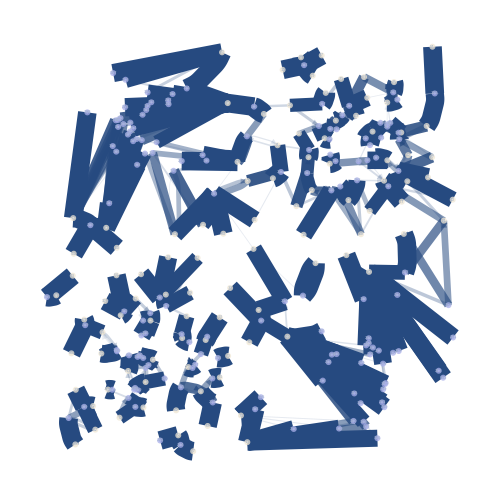

```mathematica
classesNumber = 2;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[siteType//Length],siteType}];
edgeshape2[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]}
(* here is where graph is defined, with *)
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[mosMatrix[[;;-2,;;-2]],10^-1.5],
ToString /@ Range[Length[Chop[mosMatrix[[;;-2,;;-2]],10^-1.5]]]
   }, .5,
VertexStyle->stylesListType,
VertexCoordinates->mosHabitats,
VertexSize ->2,(*vertexSize,*)
VertexLabelStyle->.1,(*vertexLabelSize,*)
ImageSize->500,
LineThickness->.015,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

1.030 | -16.400 | -6.760 | -3.180 |  5.480 |  1.360 |  1.000 | -3.010 | -10.700 | -28.800 | -0.115 | -0.795 |  30.000 |  26.000 |  0.502 |  4.470
Source | Sink | Sink | Sink | Source | Source | Source | Sink | Sink | Sink | Bridge | Sink | Source | Source | Source | Source

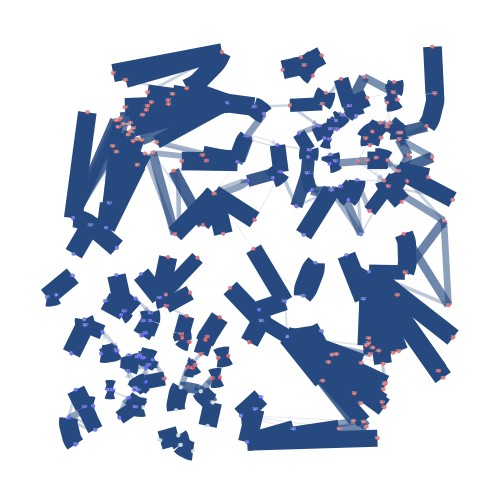

```mathematica
gridSourceSink=Grid[{
Style[PaddedForm[#,{3,3}],7.5,Bold]&/@outMinusIn,
Style[#,7.5,Bold]&/@typeOfCommunity
},
Frame->True,Background->{Lighter[#,0.1]&/@colors[[1;;Length[outMinusIn]]],None},ItemSize->3]
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
flattenedRatios=Table[ConstantArray[typeOfCommunity[[i]],communities[[i]]//Length],{i,1,communities//Length}]//Flatten;
graphSinkSource=HighlightGraph[graph, Style[#[[2]] ,
Directive[EdgeForm[Directive[Opacity[.75],
Switch[#[[3]],
"Bridge",Lighter[White,0],
"Sink",Lighter[Blue,0.3],
"Source",Lighter[Red,0.3]
],Thickness[.0025]]],#[[1]]]
] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)]
```

```mathematica
(* 1. Cluster Centroids *)
clusterCentroids = Mean[#]&/@clusteredCoordinates;
(* 2. Net flows between clsuters *)
clusterFlows = Table[Total[transitions[[communities[[j]],communities[[i]]]],2],{i,1,Length[communities]},{j,1,Length[communities]}];
clusterFlows = ReplacePart[clusterFlows,{i_,i_}->0];
```

{1,3,3,3,1,1,1,3,3,3,2,3,1,1,1,1}

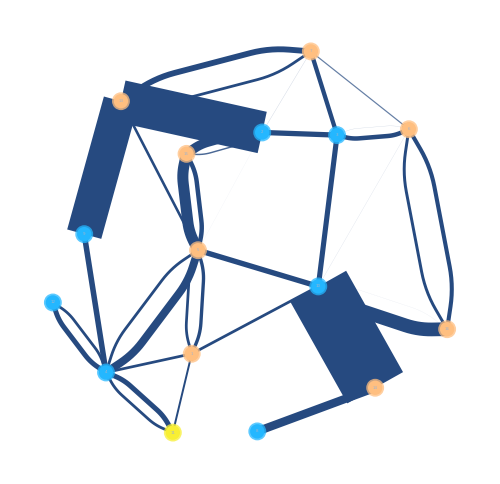

```mathematica
(* 3. Plot *)
differenceThreshold= .3;
clusterType=If[Abs[#]<differenceThreshold,2,If[#>0,1,3]]&/@outMinusIn

classesNumber = 3; (* Sources, sinks, bridges *)
colorsType=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[clusterType//Length],clusterType}];
edgeshape2[e_,___]:={Arrowheads[{{.02,.75}}],Arrow[e]}
(* here is where graph is defined, with *)
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[clusterFlows,10^-1.5],
ToString /@ Range[Length[Chop[clusterFlows,10^-1.5]]]
   }, .5,
VertexStyle->stylesListType,
VertexCoordinates->clusterCentroids,
VertexSize ->.2,(*vertexSize,*)
VertexLabelStyle->0.01,(*vertexLabelSize,*)
ImageSize->500,
LineThickness->.002,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

```mathematica
(* Plot Side-by-Side the symmetric and asymmetric flows on this network *)
asymFlow =Table[If[#>0,#,0]&/@i,{i,clusterFlows - Transpose[clusterFlows]}];
symFlow = clusterFlows-asymFlow;
```

```mathematica
edgeshape1[e_,___]:={Arrowheads[{{0,1}}],Arrow[e]}
graph1 = GraphTransitionsFrequenciesWithMax[
  {
Chop[UpperTriangularize[symFlow],10^-1.5],
ToString /@ Range[Length[Chop[UpperTriangularize[symFlow],10^-1.5]]]
   }, .5,
VertexStyle->stylesListType,
VertexCoordinates->clusterCentroids,
VertexSize ->.2,(*vertexSize,*)
VertexLabelStyle->0.01,(*vertexLabelSize,*)
ImageSize->300,
LineThickness->.003,
EdgeShapeFunction->edgeshape1,
VariableStyle->"Both"
  ];
edgeshape2[e_,___]:={Arrowheads[{{.05,.75}}],Arrow[e]}
graph2 = GraphTransitionsFrequenciesWithMax[
  {
Chop[asymFlow,10^-1.5],
ToString /@ Range[Length[Chop[asymFlow,10^-1.5]]]
   }, .5,
VertexStyle->stylesListType,
VertexCoordinates->clusterCentroids,
VertexSize ->.2,(*vertexSize,*)
VertexLabelStyle->0.01,(*vertexLabelSize,*)
ImageSize->300,
LineThickness->.003,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ];
```

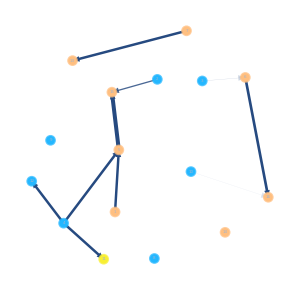
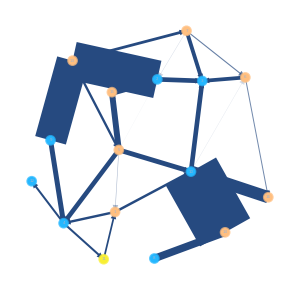

```mathematica
{graph1,graph2}
```

```mathematica
(* Check: when we sum over the columns and rows of h, do we get the inCommunity and outCommunity vectors that Hector calculated above *)
Total[ReplacePart[clusterFlows,{i_,i_}->0]]
inCommunity
Total[ReplacePart[clusterFlows,{i_,i_}->0]//Transpose]
outCommunity
```

{1.93495,18.8501,6.90925,7.78918,4.51909,1.71985,2.11518,3.00646,12.7232,30.8601,1.82275,1.78493,0.996974,0.000649429,4.49764,1.53454}

{1.93495,18.8501,6.90925,7.78918,4.51909,1.71985,2.11518,3.00646,12.7232,30.8601,1.82275,1.78493,0.996974,0.000649429,4.49764,1.53454}

{2.96692,2.41693,0.152047,4.60571,10.,3.08022,3.11541,0.00134078,2.00017,2.02778,1.70803,0.99025,31.,26.,5.,6.}

{2.96692,2.41693,0.152047,4.60571,10.,3.08022,3.11541,0.00134078,2.00017,2.02778,1.70803,0.99025,31.,26.,5.,6.}

### Manipulating the VCI matrix using our clustering

```mathematica
(* Try some clustering, based on neighborhood contraction *)
clusteredCoordinates=FindClusters[mosHabitats,Method->"NeighborhoodContraction"];
(* List of site indices *)
clustersStrings=Table[ToString/@Flatten[Position[mosHabitats,#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}];
(* Vector of site IDs for each site *)
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[mosHabitats]];
(* Out-connectedness vs In-connectedness between clusters *)
outCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[migrationDimensionalMatrix,{i_,i_}->0];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[migrationDimensionalMatrix,{i_,i_}->0]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
```

```mathematica
vci = vciAnalytic[ms, init, EIP,siteType];
(* Total VC for each spot *)
Total[vci[[;;nHouses]]//Transpose]
(*Chop[vci[[;;nHouses,;;nHouses]],edgeChopThreshold]//TraditionalForm*)
```

{0.15563,0.0168962,0.14792,0.172916,0.0668245,0.00227982,0.000255956,0.0145495,0.00500721,0.0439795,0.0000160817,0.00361672,0.0000164016,0.0413025,0.00325373,0.000116463,0.206979,4.25603×10^-7,9.17627×10^-7,0.0224537,2.72372×10^-6,0.0000277221,0.0353851,0.168865,0.0000620152,0.115344,0.011375,0.0739964,0.0549948,0.107903,0.00567905,2.261×10^-7,0.0537045,0.0591769,0.0489158,0.000117811,0.003349,0.122247,0.000836958,3.12937×10^-7,0.00203082,4.32269×10^-8,6.95052×10^-6,0.111691,3.28695×10^-8,0.106726,0.000267842,0.187926,0.107833,0.0526572,0.000028373,0.227496,0.0675847,0.000242064,0.0887221,0.0362118,0.0116701,0.146896,0.000908192,0.640195,0.0666148,0.103558,1.20205×10^-6,4.53244×10^-8,1.4463×10^-6,7.81627×10^-7,0.35279,0.258579,0.31188,0.0000302283,0.00156358,0.102027,0.804135,0.109346,0.00102403,0.303401,0.0000837077,0.114478,0.121901,0.0238806,0.00398357,0.00247346,0.000160725,0.00155155,0.138763,0.1236,1.12422×10^-6,0.971985,0.0000170713,0.882624,0.0283553,0.00065961,5.10573×10^-6,0.0575674,0.179527,0.0522491,0.0131903,0.00023848,0.00544147,0.0000368467}

```mathematica
(* Which of the sites count as sources?
Categorize by type of community *)
differenceThreshold = 0.3;
outMinusIn=outCommunity-inCommunity;
typeOfCommunity=If[Abs[#]<differenceThreshold,"Bridge",If[#>0,"Source","Sink"]]&/@outMinusIn
clusterType=If[Abs[#]<differenceThreshold,2,If[#>0,1,3]]&/@outMinusIn
```

{Source,Sink,Sink,Sink,Source,Source,Source,Sink,Sink,Sink,Bridge,Sink,Source,Source,Source,Source}

{1,3,3,3,1,1,1,3,3,3,2,3,1,1,1,1}

```mathematica
(* Let's try adding pesticides to the egg laying sites in some of the source locations *)
(* Step 1: identify which of the sources are egg laying sites *)
(*communities[[Position[clusterType, 1]//Flatten]]
Position[siteType,1]//Flatten*)
sourceFeedingSites = Intersection[Position[siteType,1]//Flatten, communities[[Position[clusterType, 1]//Flatten]]//Flatten]
```

{1,5,7,8,9,11,12,13,16,19,22,25,26,27,28,29,32,33,35,38,40,42,44,45,46,47,51,57,68,69,70,71,74,75,77,78,80,81,84,87,89,91,93,96,98}

```mathematica
(* Adding in mosquito death *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
(* vaccinate our feeding site sources *)
mosHazardRates[[sourceFeedingSites]] = 0.5;
mosMatrixInsecticide = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msInsecticide = mosMatrixInsecticide[[;;-2,;;-2]];
```

```mathematica
vciInsecticide = vciAnalytic[msInsecticide, init, EIP,siteType];
(* Total VC for each spot *)
Total[vci[[;;nHouses]]//Transpose];
Total[vciInsecticide[[;;nHouses]]//Transpose];
```

```mathematica
(* And what about random assignment of insecticide? *)
SeedRandom[6];
sourceFeedingSitesRandom= RandomSample[Position[siteType,1]//Flatten,Length[sourceFeedingSites]]//Sort

mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
(* vaccinate our feeding site sources *)
mosHazardRates[[sourceFeedingSitesRandom]] = 0.5;
mosMatrixRandom = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msRandom = mosMatrixRandom[[;;-2,;;-2]];
```

{1,3,4,5,6,7,9,11,13,14,16,18,19,23,26,27,29,30,31,32,33,35,36,41,45,47,50,52,55,56,58,61,65,68,69,70,71,74,75,84,89,91,92,98,99}

```mathematica
vciRandom = vciAnalytic[msRandom, init, EIP,siteType];
(* Total VC for each spot *)
Total[vci[[;;nHouses]]//Transpose];
Total[vciRandom[[;;nHouses]]//Transpose];
```

```mathematica
(* 
Compare total change in VC to baseline 
Note that random does a little better than targeted
*)
Total[vci,2]
Total[vciInsecticide,2]
Total[vciRandom,2]
Total[vci//Transpose];
Total[vciInsecticide//Transpose];
Total[vciRandom//Transpose];
```

8.69281

6.66928

5.79105

## Analysis: Attacking Individual Nodes based on VCI

It looks as though the clustering methods that we used to determine “sources and sinks” aren’t very meaningful in this context.  But what is meaningful is that apparently we can attack individual nodes based on their VCI
Let’s now focus on how attacking nodes based on VCI might be a good first pass at a strategy

### Simplest case - small landscape with 2 clusters of houses

```mathematica
(* Read in data *)
mosHabitats = Import["/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron/MosHabitats.csv"];
siteType = If[#=="houses",1,2]&/@mosHabitats[[2;;,2]];
mosHabitats = 5000*mosHabitats[[2;;, 3;;]];
nHouses = Count[siteType,1];
```

```mathematica
networkDimension = 2; (* Two types of sites for now *)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(* Define which inter-type transitions are allowed *)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@siteType,{i,siteType}]; 
(* Calculate distances between everything, and movement probabilities *)
euclideanDistances = CalculateEuclideanDistances[mosHabitats];
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(* Re-weighting all edges according to the movement kernel and penalization mask.*)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
```

```mathematica
(* Initial conditions: everything starts the same everywhere *)
(*init = Join[Table[1./Length[migrationDimensionalMatrix],{i,1,Length[migrationDimensionalMatrix]}],{0}];*)
init =#&/@If[#==1,0.,1.]&/@siteType/Count[siteType,2];
init = Join[init,{0}];
EIP = 10;
```

```mathematica
(* Baseline Case: No insecticide *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vci = vciAnalytic[ms, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vci[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{0.173856,0.0780949}

```mathematica
(*Adding Insecticide*)
nInsecticideSites = 10;
```

```mathematica
(* Case 2: Random Insecticide*)
SeedRandom[21];
randomSites = RandomSample[Position[siteType,1]//Flatten, nInsecticideSites]//Sort
(*Calculate Matrix*)mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosHazardRates[[randomSites]] = 0.2;
mosMatrixRandom = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msRandom = mosMatrixRandom[[;;-2,;;-2]];
(* VCI Calculation *)
vciRandom = vciAnalytic[msRandom, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vciRandom[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{1,3,7,9,18,24,25,26,36,43}

{0.137424,0.0582546}

```mathematica
(* Case 3: Sorting by highest VC *)
h = Total[vci[[;;nHouses]]//Transpose];
orderedSites = Ordering[h,-nInsecticideSites]//Sort
(*Calculate Matrix*)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosHazardRates[[orderedSites]] = 0.2;
mosMatrixOrdered = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msOrder = mosMatrixOrdered[[;;-2,;;-2]];
(* VCI Calculation *)
vciOrder = vciAnalytic[msOrder, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vciOrder[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{4,9,10,19,20,25,29,37,43,48}

{0.0769097,0.00741263}

```mathematica
c1 = Total[vci[[;;nHouses,;;nHouses]]//Transpose];
c2 =Total[vciOrder[[;;nHouses,;;nHouses]]//Transpose];
c3 = Total[vciRandom[[;;nHouses,;;nHouses]]//Transpose];
(* Absolute and fractional size of decrease*)
MatrixForm[{orderedSites,(c1-c2)[[orderedSites]], (c1-c2)[[orderedSites]]/c1[[orderedSites]]}]
MatrixForm[{randomSites,(c1-c3)[[randomSites]], (c1-c3)[[randomSites]]/c1[[randomSites]]}]
(* Mean fractinal change *)
{Mean[(c1-c2)/c1], StandardDeviation[(c1-c2)/c1]}
{Mean[(c1-c3)/c1],StandardDeviation[(c1-c3)/c1] }
```

(4 | 9 | 10 | 19 | 20 | 25 | 29 | 37 | 43 | 48
0.264086 | 0.477331 | 0.242117 | 0.676677 | 0.410333 | 0.626652 | 1.05601 | 0.216051 | 0.394241 | 0.223905
0.684664 | 0.752745 | 0.716054 | 0.768638 | 0.740091 | 0.752291 | 0.742933 | 0.717531 | 0.698779 | 0.752074)

(1 | 3 | 7 | 9 | 18 | 24 | 25 | 26 | 36 | 43
0.000421047 | 0.0597101 | 0.00670511 | 0.477106 | 0.00359093 | 0.0227382 | 0.627284 | 0.0196458 | 8.35668×10^-7 | 0.347559
0.129116 | 0.485044 | 0.293415 | 0.752391 | 0.173437 | 0.545383 | 0.753049 | 0.453735 | 0.223215 | 0.616036)

{0.332887,0.353496}

{0.144441,0.211323}

### Next case - larger landscape with 4 clusters of houses, 2 clusters mosquitoes

```mathematica
(* Read in data *)
mosHabitats = Import["/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron/MosHabitats_2.csv"];
siteType = If[#=="houses",1,2]&/@mosHabitats[[2;;,2]];
mosHabitats = 5000*mosHabitats[[2;;, 3;;]];
nHouses = Count[siteType,1];
```

```mathematica
networkDimension = 2; (* Two types of sites for now *)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(* Define which inter-type transitions are allowed *)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@siteType,{i,siteType}]; 
(* Calculate distances between everything, and movement probabilities *)
euclideanDistances = CalculateEuclideanDistances[mosHabitats];
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(* Re-weighting all edges according to the movement kernel and penalization mask.*)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
```

```mathematica
(* Initial conditions: everything starts the same everywhere *)
(*init = Join[Table[1./Length[migrationDimensionalMatrix],{i,1,Length[migrationDimensionalMatrix]}],{0}];*)
init =#&/@If[#==1,0.,1.]&/@siteType/Count[siteType,2];
init = Join[init,{0}];
EIP = 10;
```

```mathematica
(* Baseline Case: No insecticide *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vci = vciAnalytic[ms, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vci[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{0.0869281,0.0282687}

```mathematica
(*Adding Insecticide*)
nInsecticideSites = 10;
```

```mathematica
(* Case 2: Random Insecticide*)
SeedRandom[12];
randomSites = RandomSample[Position[siteType,1]//Flatten, nInsecticideSites]//Sort
(*Calculate Matrix*)mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosHazardRates[[randomSites]] = 0.2;
mosMatrixRandom = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msRandom = mosMatrixRandom[[;;-2,;;-2]];
(* VCI Calculation *)
vciRandom = vciAnalytic[msRandom, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vciRandom[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{3,19,26,41,58,71,75,79,82,93}

{0.0752229,0.0224318}

```mathematica
(* Case 3: Sorting by highest VC *)
h = Total[vci[[;;nHouses]]//Transpose];
orderedSites = Ordering[h,-nInsecticideSites]//Sort
(*Calculate Matrix*)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosHazardRates[[orderedSites]] = 0.2;
mosMatrixOrdered = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msOrder = mosMatrixOrdered[[;;-2,;;-2]];
(* VCI Calculation *)
vciOrder = vciAnalytic[msOrder, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vciOrder[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{2,8,15,19,27,32,44,50,62,93}

{0.046585,0.00454784}

```mathematica
c1 =Total[vci[[;;nHouses,;;nHouses]]//Transpose];
c2 =Total[vciOrder[[;;nHouses,;;nHouses]]//Transpose];
c3 = Total[vciRandom[[;;nHouses,;;nHouses]]//Transpose];
(* Absolute and fractional size of decrease*)
MatrixForm[{orderedSites,(c1-c2)[[orderedSites]], (c1-c2)[[orderedSites]]/c1[[orderedSites]]}]
MatrixForm[{randomSites,(c1-c3)[[randomSites]], (c1-c3)[[randomSites]]/c1[[randomSites]]}]
(* Mean fractional change *)
{Mean[(c1-c2)/c1], StandardDeviation[(c1-c2)/c1]}
{Mean[(c1-c3)/c1],StandardDeviation[(c1-c3)/c1] }

Total[c1]
Total[c2]
Total[c3]
```

(2 | 8 | 15 | 19 | 27 | 32 | 44 | 50 | 62 | 93
0.282937 | 0.246166 | 0.332847 | 0.33934 | 0.793401 | 0.317058 | 0.334004 | 0.321574 | 0.423635 | 0.444248
0.743546 | 0.705275 | 0.738699 | 0.746415 | 0.748614 | 0.741004 | 0.71605 | 0.748379 | 0.741881 | 0.760779)

(3 | 19 | 26 | 41 | 58 | 71 | 75 | 79 | 82 | 93
4.63569×10^-20 | 0.337275 | 0.0439195 | 8.11864×10^-15 | 3.4526×10^-9 | 2.62723×10^-7 | 3.67013×10^-23 | 2.25241×10^-27 | 0.16728 | 0.390661
0.252846 | 0.741874 | 0.744328 | 0.111111 | 0.111112 | 0.111162 | 0.111119 | 0.111111 | 0.742098 | 0.669011)

{0.117241,0.251251}

{0.0732288,0.198228}

8.69281

4.6585

7.52229

### Next case - larger landscape with 2 clusters of houses, 4 clusters mosquitoes

```mathematica
(* Read in data *)
mosHabitats = Import["/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron/MosHabitats_3.csv"];
siteType = If[#=="houses",1,2]&/@mosHabitats[[2;;,2]];
mosHabitats = 5000*mosHabitats[[2;;, 3;;]];
nHouses = Count[siteType,1];
```

```mathematica
networkDimension = 2; (* Two types of sites for now *)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(* Define which inter-type transitions are allowed *)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@siteType,{i,siteType}]; 
(* Calculate distances between everything, and movement probabilities *)
euclideanDistances = CalculateEuclideanDistances[mosHabitats];
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(* Re-weighting all edges according to the movement kernel and penalization mask.*)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
```

```mathematica
(* A beautiful plot *)
colors = ColorData["BrightBands", #]&/@Range[0,1,1]//Flatten;
ListPlot[mosHabitats[[Position[siteType,#]//Flatten]]&/@{1,2}, PlotStyle->colors,PlotTheme->{"Grid","Frame"}]
```

-Graphics-

```mathematica
(* Initial conditions: everything starts the same everywhere *)
init = Join[Table[1./Length[migrationDimensionalMatrix],{i,1,Length[migrationDimensionalMatrix]}],{0}];
(*init =#&/@If[#==1,0.,1.]&/@siteType/Count[siteType,2];
init = Join[init,{0}];*)
EIP = 10;
```

```mathematica
(* Baseline Case: No insecticide *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vci = vciAnalytic[ms, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vci[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{0.0907762,0.0179619}

```mathematica
(*Adding Insecticide*)
nInsecticideSites = 10;
```

```mathematica
(* Case 2: Random Insecticide*)
SeedRandom[20];
randomSites = RandomSample[Position[siteType,1]//Flatten, nInsecticideSites]//Sort
(*Calculate Matrix*)mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosHazardRates[[randomSites]] = 0.2;
mosMatrixRandom = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msRandom = mosMatrixRandom[[;;-2,;;-2]];
(* VCI Calculation *)
vciRandom = vciAnalytic[msRandom, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vciRandom[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{1,44,45,47,64,71,79,80,83,91}

{0.0854775,0.0175623}

```mathematica
(* Case 3: Sorting by highest VC *)
h = Total[vci[[;;nHouses]]//Transpose];
orderedSites = Ordering[h,-nInsecticideSites]//Sort
(*Calculate Matrix*)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosHazardRates[[orderedSites]] = 0.2;
mosMatrixOrdered = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
msOrder = mosMatrixOrdered[[;;-2,;;-2]];
(* VCI Calculation *)
vciOrder = vciAnalytic[msOrder, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vciOrder[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{26,44,60,67,69,73,76,86,88,90}

{0.0554337,0.00374652}

```mathematica
c1 =Total[vci[[;;nHouses,;;nHouses]]//Transpose];
c2 =Total[vciOrder[[;;nHouses,;;nHouses]]//Transpose];
c3 = Total[vciRandom[[;;nHouses,;;nHouses]]//Transpose];
(* Absolute and fractional size of decrease*)
MatrixForm[{orderedSites,(c1-c2)[[orderedSites]], (c1-c2)[[orderedSites]]/c1[[orderedSites]]}]
MatrixForm[{randomSites,(c1-c3)[[randomSites]], (c1-c3)[[randomSites]]/c1[[randomSites]]}]
(* Mean fractional change *)
{Mean[(c1-c2)/c1], StandardDeviation[(c1-c2)/c1]}
{Mean[(c1-c3)/c1],StandardDeviation[(c1-c3)/c1] }

(* Total change *)
Total[c1]
Total[c2]
Total[c3]
```

(26 | 44 | 60 | 67 | 69 | 73 | 76 | 86 | 88 | 90
0.174087 | 0.159823 | 0.324611 | 0.195952 | 0.240502 | 0.479847 | 0.187191 | 0.159217 | 0.530738 | 0.477979
0.739648 | 0.727826 | 0.665125 | 0.6991 | 0.73844 | 0.74381 | 0.742756 | 0.744086 | 0.743589 | 0.742384)

(1 | 44 | 45 | 47 | 64 | 71 | 79 | 80 | 83 | 91
0.111032 | 0.162968 | 0.000822029 | 0.000940964 | 0.000812391 | 0.000975477 | 0.0997004 | 0.00259988 | 0.000826852 | 0.0289507
0.741062 | 0.742149 | 0.112431 | 0.116837 | 0.111112 | 0.114105 | 0.710466 | 0.118577 | 0.111312 | 0.485597)

{0.246267,0.275118}

{0.0721848,0.165339}

9.07762

5.54337

8.54775

## Analysis: VCI as Network Representation

Let’s now focus on the idea that the VCI is itself an interaction network.  This is a natural combination of the geographical representation of the landscape and the mathematical model of counting secondary bites.

### Clustering

```mathematica
(* Use Igraph *)
<<IGraphM`
```

IGCommunitiesWalktrap::shdw: Symbol IGCommunitiesWalktrap appears in multiple contexts {IGraphM`,Global`}; definitions in context IGraphM` may shadow or be shadowed by other definitions.

IGraph/M 0.3.99.1 (May 1, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
(* Read in data *)
mosHabitats = Import["/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron/MosHabitats_3.csv"];
siteType = If[#=="houses",1,2]&/@mosHabitats[[2;;,2]];
mosHabitats = 5000*mosHabitats[[2;;, 3;;]];
nHouses = Count[siteType,1];
```

```mathematica
networkDimension = 2; (* Two types of sites for now *)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(* Define which inter-type transitions are allowed *)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@siteType,{i,siteType}]; 
(* Calculate distances between everything, and movement probabilities *)
euclideanDistances = CalculateEuclideanDistances[mosHabitats];
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(* Re-weighting all edges according to the movement kernel and penalization mask.*)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
```

```mathematica
(* Initial conditions: everything starts the same everywhere *)
(*init = Join[Table[1./Length[migrationDimensionalMatrix],{i,1,Length[migrationDimensionalMatrix]}],{0}];*)
init =#&/@If[#==1,0.,1.]&/@siteType/Count[siteType,2];
init = Join[init,{0}];
EIP = 10;
```

```mathematica
(* Baseline Case: No insecticide *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vci = vciAnalytic[ms, init, EIP,siteType];
(* Variation in total VC across the different nodes *)
Total[vci[[;;nHouses,;;nHouses]]//Transpose];
{Mean[%],Variance[%]}
```

{0.0869281,0.0295059}

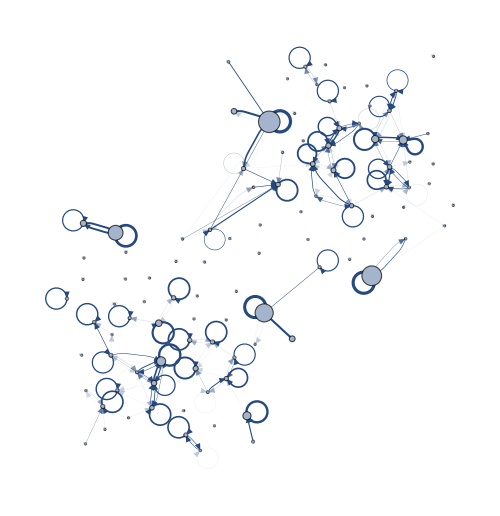

```mathematica
m =Log[1+100*Chop[vci[[;;nHouses,;;nHouses]],0.001]];
(*m =ReplacePart[m,Position[m,x_/;x>0]->1];*)
vertexSize = Total[vci[[;;nHouses,;;nHouses]]//Transpose];
vertexSize=Table[ToString[i]->Chop[vertexSize[[i]],.001]+.1,{i,1,nHouses}];

edgeshape2[e_,___]:={Arrowheads[{{.02,.75}}],Arrow[e]}
(* here is where graph is defined, with *)
graph = GraphTransitionsFrequenciesWithMax[
  {
m,
ToString /@ Range[Length[m]]
   }, .5,
(*VertexStyle->stylesListType,*)
VertexCoordinates->mosHabitats[[;;nHouses]],
VertexSize ->vertexSize,
VertexLabelStyle->.1,(*vertexLabelSize,*)
ImageSize->500,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

```mathematica
m = Chop[vci[[;;nHouses,;;nHouses]],0.0001];
mh = ReplacePart[m, Position[m, 0]->∞];
g = WeightedAdjacencyGraph[Round[mh*10000], DirectedEdges->True]
```

-Graphics-

```mathematica
(* Requires iGraph*)
g1Nodes = (WeaklyConnectedComponents[g]//Sort//Reverse)[[1]];
g1 = WeightedAdjacencyGraph[Round[10000*mh[[g1Nodes, g1Nodes]]],DirectedEdges->True]
WeightedAdjacencyMatrix[g1]//MatrixForm;
```

-Graphics-

```mathematica
cWalktrap = IGCommunitiesWalktrap[g];
cCommunities = cWalktrap["Communities"]//Sort//Reverse
```

{{2,3,5,7,8,12,20,23,24,27,28,29,30,31,35,36,38,44,49,57,58,59,68,69,75,80,81,84,85,86,88,90,91,95},{1,4,6,10,14,15,26,33,39,41,46,48,50,52,53,55,56,61,67,71,73,74,76,79},{37,62,82,99},{17,54,60,83},{9,16,47,96},{78,98},{72,97},{34,92},{100},{94},{93},{89},{87},{77},{70},{66},{65},{64},{63},{51},{45},{43},{42},{40},{32},{25},{22},{21},{19},{18},{13},{11}}

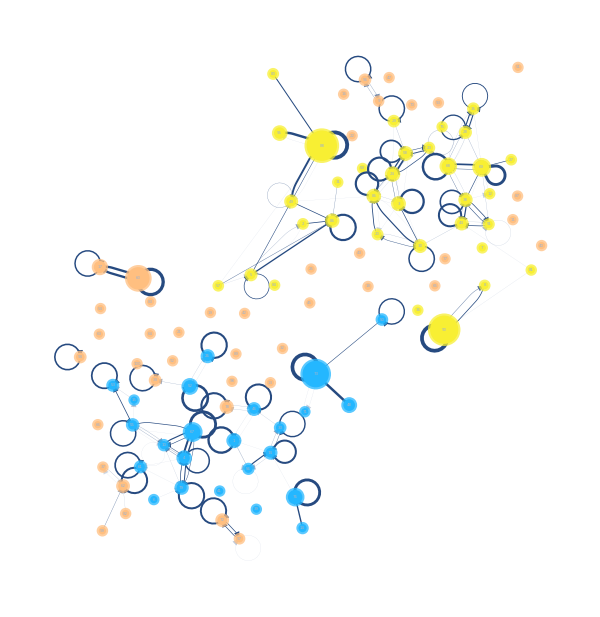

```mathematica
(* Make a beautiful plot of our geographical clusters *)
(* First, assign site types to each of our communities *)
cCommunities = cWalktrap["Communities"]//Sort//Reverse;
commType = Table[1,{i,Range[nHouses]}];
commType[[cCommunities[[1]]]] = 2;
commType[[cCommunities[[2]]]] = 3;
(*commType[[cCommunities[[3]]]] = 4;
commType[[cCommunities[[4]]]] = 5;
commType[[cCommunities[[5]]]] = 6;*)
(* Translate style of graph *)
classesNumber = Length[DeleteDuplicates[commType]];
colorsType=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[commType//Length],commType}];
m =Log[1+100*Chop[vci[[;;nHouses,;;nHouses]],0.001]];
(*m =ReplacePart[m,Position[m,x_/;x>0]->1];*)
vertexSize = Total[vci[[;;nHouses,;;nHouses]]//Transpose];
vertexSize=Table[ToString[i]->Chop[vertexSize[[i]],.001]+.3,{i,1,nHouses}];
edgeshape2[e_,___]:={Arrowheads[{{.02,.75}}],Arrow[e]}
(* Create the graph! *)
graph = GraphTransitionsFrequenciesWithMax[
  {
m,
ToString /@ Range[Length[m]]
   }, .5,
VertexStyle->stylesListType,
VertexCoordinates->mosHabitats[[;;nHouses]],
VertexSize ->vertexSize,
VertexLabelStyle->.1,(*vertexLabelSize,*)
ImageSize->600,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

### Try: Source-Sink analysis?

```mathematica
cCommunities[[;;4]]
```

{{2,3,5,7,8,12,20,23,24,27,28,29,30,31,35,36,38,44,49,57,58,59,68,69,75,80,81,84,85,86,88,90,91,95},{1,4,6,10,14,15,26,33,39,41,46,48,50,52,53,55,56,61,67,71,73,74,76,79},{37,62,82,99},{17,54,60,83}}

```mathematica
communities=cCommunities;
outCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[ vci[[;;nHouses,;;nHouses]],{i_,i_}->0];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[vci[[;;nHouses,;;nHouses]],{i_,i_}->0]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
```

```mathematica
(* They are all bridges! *)
outCommunity
inCommunity
```

{0.000500134,0.0083732,0.00080252,1.17993×10^-6,0.0000361982,0.00349455,0.000057471,0.000998788,0.0000368248,1.58444×10^-6,5.10566×10^-6,0.0000170698,1.12422×10^-6,0.0000837024,0.0000302254,7.8162×10^-7,1.4463×10^-6,4.53244×10^-8,1.20202×10^-6,0.000028373,3.28695×10^-8,6.95048×10^-6,4.32269×10^-8,3.12937×10^-7,2.261×10^-7,0.0000620032,0.0000277204,2.72365×10^-6,9.17627×10^-7,4.25603×10^-7,0.0000163991,0.0000160809}

{0.000313896,0.00558311,0.0000675512,8.00327×10^-6,0.000152054,0.00379257,0.00010892,0.00439145,0.0000390677,2.37867×10^-6,3.24508×10^-6,0.0000112185,7.69081×10^-7,0.0000235198,0.0000163447,8.9204×10^-7,9.89745×10^-7,4.86755×10^-8,1.20713×10^-6,9.05998×10^-10,1.65702×10^-8,3.5421×10^-6,5.07216×10^-9,1.11268×10^-11,2.14007×10^-7,0.0000176628,0.000034053,2.95852×10^-6,1.81444×10^-8,3.43943×10^-7,0.00001853,0.000010781}

## Analysis: Adding Wind

What we've found so far all seems to suggest that there isn’t a lot of long-distance net transfer of malaria from one part of the map to another: 
• Using geographical clustering to determine sources and sinks and attacking the sources is less effective than a random distribution of insecticide.
• Using network-based clustering on the VCI matrix seems to indicate that the clusters have no net flow of malaria in or out

We can try explicitly adding a bias to the migration matrix and repeating our analyses, to see whether adding “wind” that blows mosquitoes from North to South changes anything

### Reading in data, adding wind

```mathematica
(* Read in data *)
mosHabitats = Import["/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron/MosHabitats_2.csv"];
siteType = If[#=="houses",1,2]&/@mosHabitats[[2;;,2]];
mosHabitats = 5000*mosHabitats[[2;;, 3;;]];
nHouses = Count[siteType,1];
```

```mathematica
networkDimension = 2; (* Two types of sites for now *)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(* Define which inter-type transitions are allowed *)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@siteType,{i,siteType}]; 
(* Calculate distances between everything, and movement probabilities *)
euclideanDistances = CalculateEuclideanDistances[mosHabitats];
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(* Re-weighting all edges according to the movement kernel and penalization mask.*)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
```

```mathematica
(* Re-weighting based on northward wind, by adjusting using the cosine between directional vectors *)
windMigrationProbabilities = Table[
z = mosHabitats[[j]] - mosHabitats[[i]];
cosineAdjustment = ((z[[2]]/Sqrt[z[[1]]^2 + z[[2]]^2])//Quiet)/.Indeterminate->0;
migrationProbabilities[[i,j]]*(1+cosineAdjustment),
{i,1,Length[mosHabitats]},{j,1,Length[mosHabitats]}];
windMigrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*windMigrationProbabilities);
```

```mathematica
(* Initial conditions: everything starts the same everywhere *)
(*init = Join[Table[1./Length[migrationDimensionalMatrix],{i,1,Length[migrationDimensionalMatrix]}],{0}];*)
init =#&/@If[#==1,0.,1.]&/@siteType/Count[siteType,2];
init = Join[init,{0}];
EIP = 10;
```

```mathematica
(* Wind Case: no insecticide *)
mosHazardRates = Table[.1,{i,1,Length[windMigrationDimensionalMatrix]}];
mosMatrix = Join[Table[Join[windMigrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[windMigrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[windMigrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vciWind = vciAnalytic[ms, init, EIP,siteType];

(* Baseline Case: no insecticide *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vci = vciAnalytic[ms, init, EIP,siteType];
```

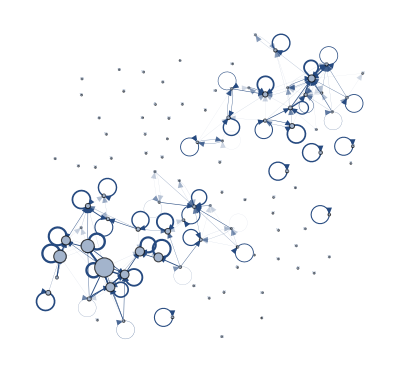
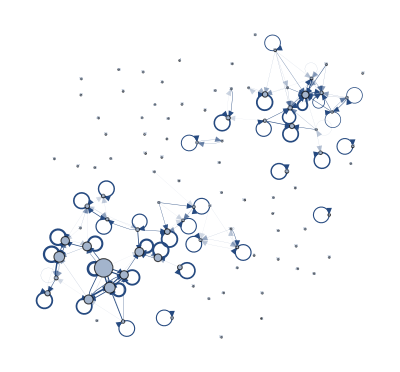

```mathematica
(* Graph 1: with wind *)
m =Log[1+100*Chop[vciWind[[;;nHouses,;;nHouses]],0.001]];
(*m =ReplacePart[m,Position[m,x_/;x>0]->1];*)
vertexSize = Total[vciWind[[;;nHouses,;;nHouses]]//Transpose];
vertexSize=Table[ToString[i]->Chop[vertexSize[[i]],.001]+.1,{i,1,nHouses}];

edgeshape2[e_,___]:={Arrowheads[{{.02,.75}}],Arrow[e]}
(* here is where graph is defined, with *)
graph1 = GraphTransitionsFrequenciesWithMax[
  {
m,
ToString /@ Range[Length[m]]
   }, .5,
(*VertexStyle->stylesListType,*)
VertexCoordinates->mosHabitats[[;;nHouses]],
VertexSize ->vertexSize,
VertexLabelStyle->.1,(*vertexLabelSize,*)
ImageSize->400,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ];
(* Graph 2: without wind *)
m =Log[1+100*Chop[vci[[;;nHouses,;;nHouses]],0.001]];
(*m =ReplacePart[m,Position[m,x_/;x>0]->1];*)
vertexSize = Total[vci[[;;nHouses,;;nHouses]]//Transpose];
vertexSize=Table[ToString[i]->Chop[vertexSize[[i]],.001]+.1,{i,1,nHouses}];

edgeshape2[e_,___]:={Arrowheads[{{.02,.75}}],Arrow[e]}
(* here is where graph is defined, with *)
graph2 = GraphTransitionsFrequenciesWithMax[
  {
m,
ToString /@ Range[Length[m]]
   }, .5,
(*VertexStyle->stylesListType,*)
VertexCoordinates->mosHabitats[[;;nHouses]],
VertexSize ->vertexSize,
VertexLabelStyle->.1,(*vertexLabelSize,*)
ImageSize->400,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ];
(* With Wind, Without Wind *)
{graph1, graph2}
```

### Comparing VCI for wind vs. no wind

```mathematica
(*
  Does the list of most vulnerable locations change?
Does the efficacy of targeting vulnerable locations change?
*)
h = Total[vci[[;;nHouses,;;nHouses]]//Transpose];
orderedSites = Ordering[h,-20]//Reverse
hWind = Total[vciWind[[;;nHouses,;;nHouses]]//Transpose];
orderedSitesWind = Ordering[hWind,-20]//Reverse
```

{27,93,62,44,19,15,50,32,2,8,17,9,82,65,42,98,81,52,66,34}

{27,15,62,19,93,2,50,32,63,17,9,98,65,82,34,44,52,81,78,20}

{1.05983,0.583939,0.571028,0.466453,0.454626,0.450585,0.429694,0.427876,0.380524,0.349036,0.251996,0.239039,0.225414,0.204015,0.193105,0.178209,0.15942,0.15753,0.140373,0.122103}

{1.11057,0.727881,0.689047,0.475613,0.470382,0.464188,0.463133,0.448965,0.350674,0.251993,0.230074,0.214656,0.20532,0.197992,0.150231,0.145459,0.135822,0.120313,0.119073,0.114027}

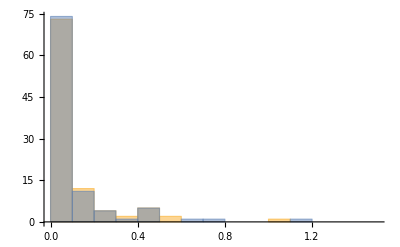

{0.0869281,0.0282687}

{0.0869281,0.031847}

```mathematica
(* Looks like we have a very slightly more skewed distribution of VCI *)
h[[orderedSites]]
hWind[[orderedSitesWind]]
Histogram[{h,hWind},{0,1.5,1.5/15}]
{Mean[h],Variance[h]}
{Mean[hWind],Variance[hWind]}
```

```mathematica
(* Calculate VCI change with attacking highest VCI sites, with and without wind *)
nInsecticideSites = 5;
(* No Wind, Insecticide *)
mosHazardRates = Table[.1,{i,1,Length[migrationDimensionalMatrix]}];
orderedSites = Ordering[ Total[vci[[;;nHouses]]//Transpose],-nInsecticideSites]//Sort;
mosHazardRates[[orderedSites]]=0.2;
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vciInsecticide= vciAnalytic[ms, init, EIP,siteType];

(* Wind, Insecticide *)
mosHazardRates = Table[.1,{i,1,Length[windMigrationDimensionalMatrix]}];
orderedSites = Ordering[ Total[vciWind[[;;nHouses]]//Transpose],-nInsecticideSites]//Sort;
mosHazardRates[[orderedSites]]=0.2;
mosMatrix = Join[Table[Join[windMigrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[windMigrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[windMigrationDimensionalMatrix]}],{1.}]},1];
ms = mosMatrix[[;;-2,;;-2]];
(* VCI Calculation *)
vciWindInsecticide = vciAnalytic[ms, init, EIP,siteType];
```

```mathematica
Chop[Total[vci//Transpose][[;;nHouses]]-Total[vciInsecticide//Transpose][[;;nHouses]],0.001]
Chop[Total[vciWind//Transpose][[;;nHouses]]-Total[vciWindInsecticide//Transpose][[;;nHouses]],0.001]
```

{0,0.00483326,0,0,0,0,0,0,0,0,0,0,0,0,0.0129753,0,0,0,0.337338,0,0.0164946,0,0,0,0,0,0.780015,0,0,0,0,0.0857322,0,0.0123604,0,0,0,0,0,0,0,0,0,0.331741,0,0,0,0,0,0.0113451,0,0,0,0,0,0,0,0,0,0,0,0.4182,0,0,0,0.0634898,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0010567,0,0,0,0,0,0,0,0,0,0,0.429401,0,0,0,0,0,0,0}

{0,0.0105988,0,0,0,0,0,0,0,0,0,0,0,0,0.550505,0,0,0,0.353974,0,0.0184174,0,0,0,0,0,0.80943,0,0,0,0,0.104315,0,0,0,0,0,0,0,0,0,0,0,0.0645314,0,0,0,0,0,0.0250506,0,0,0,0,0,0,0,0,0,0,0,0.495155,0,0,0,0.0422901,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.00213753,0,0,0,0,0,0,0,0,0,0,0.308602,0,0,0,0,0.00235547,0,0}

```mathematica
Total[vci,2]
Total[vciInsecticide,2]
Total[vciWind,2]
Total[vciWindInsecticide,2]
```

8.69281

6.18723

8.69281

5.90319

```mathematica
(* 
Very samll improvement, if any. It is possible that, again, there may be a problem in terms of defining the transitions as probabilities instead of rates.  All the wind does is skew the probabilities in favor of some connections over others. 


One thing to note here is if we return to the source- sink dynamics it might make it more obvious where the sources are.  Currently, without wind, there's no net migration across regions.  But with the wind we might actually see stronger delineations between sources and sinks.
*)
```